# Compound Poisson mutations

```mathematica
μ=1.2/2
t=59
λSol=Solve[l*t*μ==1057]
λ=l/.λSol[[1]]
```

0.6

59

{{l→29.8588}}

29.8588

```mathematica
dataDraw=RandomVariate[CompoundPoissonDistribution[λ*t,PoissonDistribution[μ]],10^5];
```

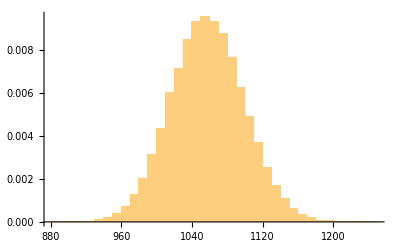

```mathematica
Histogram[dataDraw,30,"PDF"]
```